```mathematica
SetDirectory[NotebookDirectory[]]
```

```mathematica
R=0.5;
d=0.05;
α=0;
```

```mathematica
θ=π/6;
```

```mathematica
n=20;(*количество отрезков на загругленном конце лопасти*)
```

```mathematica
β=π/(n);
h= d Sin[β/2]
```

0.00392295

```mathematica
Nb=Round[π (R +d/2)/h];
```

```mathematica
C1={-R,0};C2={R,0};
```

```mathematica
β1=π/Nb;
```

```mathematica
Rup=Table[{(R+d/2)Cos[β1 i],(R+d/2)Sin[β1 i]}+C2,{i,0,Nb}];
```

```mathematica
figRup=ListPlot[Rup,PlotRange->All,AspectRatio->Automatic];
```

```mathematica
Nm=Round[π (R-d/2) /h];
```

```mathematica
β2=π/Nm;
```

```mathematica
Rdn=Reverse[Table[{(R-d/2)Cos[β2 i],(R-d/2)Sin[β2 i]}+C2,{i,0,Nm-1}]];
```

```mathematica
figRdn=ListPlot[Rdn,PlotRange->All,AspectRatio->Automatic];
```

```mathematica
Rcircle=Reverse[Table[{(d/2)Cos[β i],-(d/2)Sin[β i]}+2 C2,{i,1,n-1}]];
```

```mathematica
figRcircle=ListPlot[Rcircle,PlotRange->All,AspectRatio->Automatic];
```

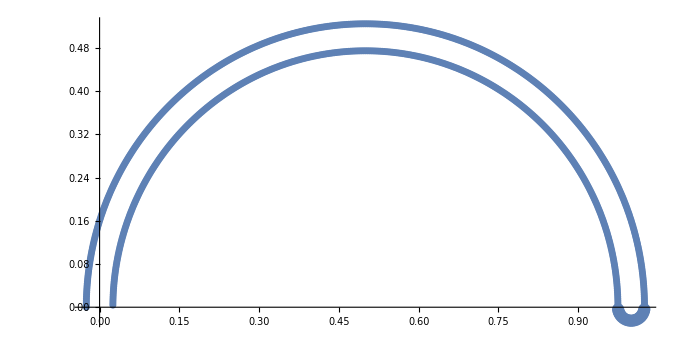

```mathematica
Show[figRup,figRdn,figRcircle,PlotRange->All]
```

```mathematica
Lup=Table[{(R-d/2)Cos[β2 i],-(R-d/2)Sin[β2 i]}+C1,{i,1,Nm}];
```

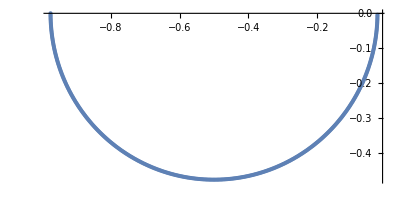

```mathematica
figLup=ListPlot[Lup,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
Ldn=Reverse[Table[{(R+d/2)Cos[β1 i],-(R+d/2)Sin[β1 i]}+C1,{i,0,Nb-1}]];
```

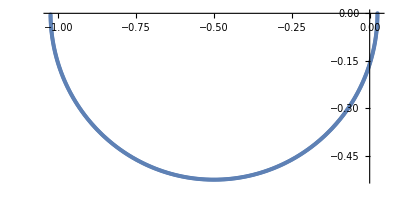

```mathematica
figLdn=ListPlot[Ldn,PlotRange->All,AspectRatio->Automatic]
```

```mathematica
Lcircle=Table[{(d/2)Cos[β i],(d/2)Sin[β i]}+2 C1,{i,1,n}];
```

```mathematica
figLcircle=ListPlot[Lcircle,PlotRange->All,AspectRatio->Automatic];
```

```mathematica
Show[figLup,figLdn,figLcircle,PlotRange->All];
```

```mathematica
AllPoints=Join[Rup,Lup,Lcircle,Ldn,Rdn,Rcircle];
```

```mathematica
Manipulate[ListPlot[AllPoints[[1;;i]],PlotRange->{{-1.1,1.1},{-0.55,0.55}}],{i,1,Length[AllPoints],1}]
```

Part::take: Cannot take positions 1 through 1 in AllPoints.

ListPlot::lpn: AllPoints⟦1;;1⟧ is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 1 in AllPoints.

ListPlot::lpn: AllPoints⟦1;;1⟧ is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 1 in AllPoints.

ListPlot::lpn: AllPoints⟦1;;1⟧ is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 1 in AllPoints.

ListPlot::lpn: AllPoints⟦1;;1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
nAll=Length[AllPoints];
```

```mathematica
AllPointsAngle=Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.AllPoints[[i]],{i,1,Length[AllPoints]}];
```

```mathematica
Manipulate[ListPlot[AllPointsAngle[[1;;i]],PlotRange->{{-2,2},{-2,2}},AspectRatio->Automatic],{i,1,Length[AllPointsAngle],1}]
```

Part::take: Cannot take positions 1 through 1 in AllPointsAngle.

ListPlot::lpn: AllPointsAngle⟦1;;1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 1 in AllPointsAngle.

ListPlot::lpn: AllPointsAngle⟦1;;1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 1 in AllPointsAngle.

ListPlot::lpn: AllPointsAngle⟦1;;1⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Export["rotor30_"<>ToString[nAll],
{"/*--------------------------------*- VM2D -*-----------------*---------------*\\
| ##  ## ##   ##  ####  #####   |                            | Version 1.11   |
| ##  ## ### ### ##  ## ##  ##  |  VM2D: Vortex Method       | 2022/08/07     |
| ##  ## ## # ##    ##  ##  ##  |  for 2D Flow Simulation    *----------------*
|  ####  ##   ##   ##   ##  ##  |  Open Source Code                           |
|   ##   ##   ## ###### #####   |  https://www.github.com/vortexmethods/VM2D  |
|                                                                             |
| Copyright (C) 2017-2022 Ilia Marchevsky, Kseniia Sokol, Evgeniya Ryatina    |
*-----------------------------------------------------------------------------*
| File name: rotor30_"<>ToString[nAll]<>StringRepeat[" ",57-StringLength@ToString[nAll]]<>"|
| Info: Rotor airfoil, angle pi/6 ("<>ToString[nAll]<>" panels)"<>StringRepeat[" ",35-StringLength@ToString[nAll]]<>"|
\\*---------------------------------------------------------------------------*/
"}~Join~{"r = {"}~Join~((ToString[SetPrecision[#,17]]<>",")&/@(AllPointsAngle[[1;;-2]]))~Join~((ToString[SetPrecision[#,17]])&/@(AllPointsAngle[[{-1}]]))~Join~{" };"},"Table"]
```

rotor30_1640